```mathematica
(*User options*)
(*Graphics options*)
ptRad=.05;(*radius of vertex dots*)
(*Grid has (0,0) at the bottom left corner and (m-1,n-1) in the upper right*)
m=20;
n=20;
(*Number of holes to poke out of the lattice*)
deletionCount=5;

(*Random walk parameters*)
walkCount=3;
walkLength=100;
```

```mathematica
(*Lattice/array helper functions*)
indexToGrid[i_]:={Mod[i-1,m],(i-1-Mod[i-1,m])/m};
gridToIndex[x_,y_]:=m*y+x+1;
```

```mathematica
(*Initialize the graph*)
(*Randomly delete some vertices*)
deletionIndices=RandomSample[Table[i,{i,m*n}],deletionCount];
(*Create the adjacency matrix*)
A=ConstantArray[0,{m*n,m*n}];
For[a=0,a<m,a++,
For[b=0,b<n,b++,
(*We are using a periodic lattice in both x and y directions, making this part easy*)
current=gridToIndex[a,b];
right=gridToIndex[Mod[a+1,m],b];
left=gridToIndex[Mod[a-1,m],b];
below=gridToIndex[a,Mod[b-1,n]];
above=gridToIndex[a,Mod[b+1,n]];
(*Check if the neighbor was deleted*)
If[!MemberQ[deletionIndices,right],A[[current]][[right]]=1];
If[!MemberQ[deletionIndices,left],A[[current]][[left]]=1];
If[!MemberQ[deletionIndices,below],A[[current]][[below]]=1];
If[!MemberQ[deletionIndices,above],A[[current]][[above]]=1];
]
]
(*Similarly, blank out the rows of deleted vertices*)
For[i=1,i≤Length[deletionIndices],i++,
A[[deletionIndices[[i]]]]=ConstantArray[0,m*n];
]
```

```mathematica
(*Power iteration algorithm approximates the dominant eigenvector*)
ev=ConstantArray[1,m*n];
(*500 is just some large enough number*)
For[i=1,i≤500,i++,
ev=N[A.ev]/Norm[A.ev]
]
(*Power iteration algorithm can sometimes produce the dominant eigenvector but it's pointing the wrong way*)
(*By Perron-Frobenius theorem, the dominant eigenvector must have all positive components. Hence we can just check the parity of the first component*)
If[ev[[1]]<0,
ev=-ev;
]
```

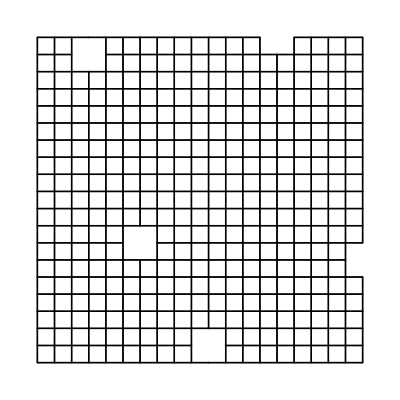

```mathematica
(*Render the graph*)
gridPoints={Black};
For[i=1,i≤Length[A],i++,
If[!MemberQ[deletionIndices,i],
AppendTo[gridPoints,Disk[indexToGrid[i],ptRad]]
]
]
gridLines={Black};
For[i=1,i≤Length[A],i++,
For[j=1,j≤Length[A],j++,
If[A[[i,j]]==1,
l={indexToGrid[i],indexToGrid[j]};
If[Norm[l[[2]]-l[[1]]]==1,
AppendTo[gridLines,Line[l]]
]
]
]
]
Show[Graphics[gridPoints],Graphics[gridLines]]
```

```mathematica
grwalks={};
merwalks={};

For[i=1,i≤walkCount,i++,
curGrWalk={};
curMerWalk={};

(*Select a starting vertex randomly.*)
start=RandomInteger[{1,m*n}];
(*Make sure we aren't starting from a deleted vertex*)
While[MemberQ[deletionIndices,start],
start=RandomInteger[{1,m*n}];
];
AppendTo[curGrWalk,indexToGrid[start]];
AppendTo[curMerWalk,indexToGrid[start]];

(*This is the main loop for the random walk process*)
grNow=start;
merNow=start;
For[j=1,j≤walkLength,j++,
(*Probe neighbors, and create a list of choices*)
nextGrChoices={};
nextMerChoices={};
(*For Maximal Entropy we have weights based on the eigenvector*)
nextMerWeights={};
For[k=1,k≤Length[A],k++,
If[A[[grNow,k]]==1,
AppendTo[nextGrChoices,k];
];
If[A[[merNow,k]]==1,
AppendTo[nextMerChoices,k];
AppendTo[nextMerWeights,ev[[k]]];
];
];

(*Select one of the choices at random*)
grNow=RandomChoice[nextGrChoices];
merNow=RandomChoice[nextMerWeights->nextMerChoices];
AppendTo[curGrWalk,indexToGrid[grNow]];
AppendTo[curMerWalk,indexToGrid[merNow]];
];
AppendTo[grwalks,curGrWalk];
AppendTo[merwalks,curMerWalk];
]
```

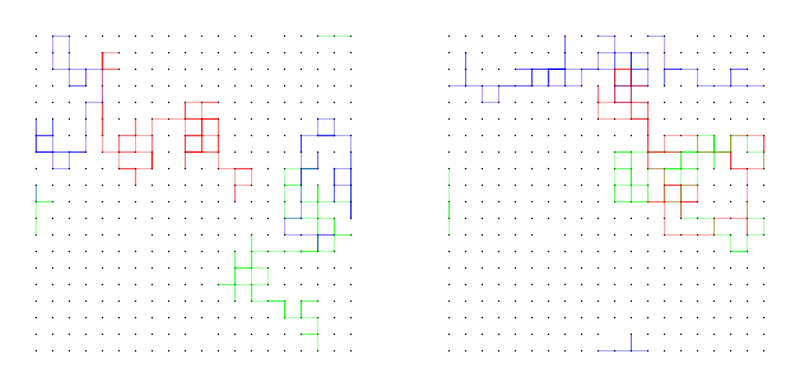

```mathematica
(*Render the walks*)
grPaths={Opacity[1/walkCount]};
merPaths={Opacity[1/walkCount]};
For[i=1,i≤walkCount,i++,
gl={Hue[i/walkCount]};
gm={Hue[i/walkCount]};
For[j=1,j≤walkLength,j++,
(*Don't render the edge when the walk wraps around the periodic lattice*)
If[Norm[grwalks[[i,j]]-grwalks[[i,j+1]]]==1,
AppendTo[gl,Line[{grwalks[[i,j]],grwalks[[i,j+1]]}]];
];
If[Norm[merwalks[[i,j]]-merwalks[[i,j+1]]]==1,
AppendTo[gm,Line[{merwalks[[i,j]],merwalks[[i,j+1]]}]];
];
];
AppendTo[grPaths,gl];
AppendTo[merPaths,gm];
];
GraphicsRow[{Show[Graphics[gridPoints],Graphics[grPaths]],Show[Graphics[gridPoints],Graphics[merPaths]]},ImageSize->Full]
```

```mathematica
(*To make a density picture, we generate enough walks to cover the lattice many times*)
walkCount=15;
walkLength=1000;
(*The following is verbatim from the earlier cell to generate walks*)
grwalks={};
merwalks={};

For[i=1,i≤walkCount,i++,
curGrWalk={};
curMerWalk={};

(*Select a starting vertex randomly.*)
start=RandomInteger[{1,m*n}];
(*Make sure we aren't starting from a deleted vertex*)
While[MemberQ[deletionIndices,start],
start=RandomInteger[{1,m*n}];
];
AppendTo[curGrWalk,indexToGrid[start]];
AppendTo[curMerWalk,indexToGrid[start]];

(*This is the main loop for the random walk process*)
grNow=start;
merNow=start;
For[j=1,j≤walkLength,j++,
(*Probe neighbors, and create a list of choices*)
nextGrChoices={};
nextMerChoices={};
(*For Maximal Entropy we have weights based on the eigenvector*)
nextMerWeights={};
For[k=1,k≤Length[A],k++,
If[A[[grNow,k]]==1,
AppendTo[nextGrChoices,k];
];
If[A[[merNow,k]]==1,
AppendTo[nextMerChoices,k];
AppendTo[nextMerWeights,ev[[k]]];
];
];

(*Select one of the choices at random*)
grNow=RandomChoice[nextGrChoices];
merNow=RandomChoice[nextMerWeights->nextMerChoices];
AppendTo[curGrWalk,indexToGrid[grNow]];
AppendTo[curMerWalk,indexToGrid[merNow]];
];
AppendTo[grwalks,curGrWalk];
AppendTo[merwalks,curMerWalk];
]
```

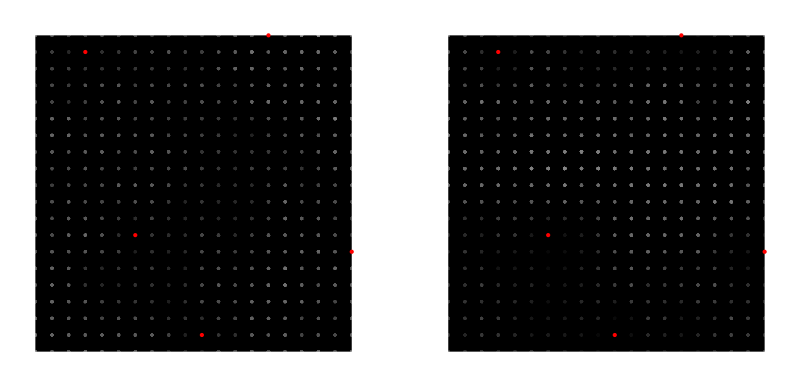

```mathematica
(*Render the density picture*)
(*First, determine an opacity scaling term: the most frequent vertex should be opacity 1*)
modegr=Commonest[Flatten[grwalks,1]][[1]];
modemerw=Commonest[Flatten[merwalks,1]][[1]];
maxgr=Count[Flatten[grwalks,1],modegr];
maxmerw=Count[Flatten[merwalks,1],modemerw];
grpts={Opacity[1./maxgr]};
merpts={Opacity[1./maxmerw]};
(*Create graphics points for each vertex hit by the walks, and stack them up. Opacity rules will take care of the rest*)
For[i=1,i≤walkCount,i++,
gp={White};
mp={White};
For[j=1,j≤walkLength+1,j++,
AppendTo[gp,Point[grwalks[[i,j]]]];
AppendTo[mp,Point[merwalks[[i,j]]]];
];
AppendTo[grpts,gp];
AppendTo[merpts,mp];
]
(*For contrast, show the deleted points as red vertices*)
deletedpts={Red};
For[i=1,i≤deletionCount,i++,
AppendTo[deletedpts,Point[indexToGrid[deletionIndices[[i]]]]];
]
GraphicsRow[{Show[Graphics[Rectangle[indexToGrid[1],indexToGrid[m*n]]],Graphics[grpts],Graphics[deletedpts]],Show[Graphics[Rectangle[indexToGrid[1],indexToGrid[m*n]]],Graphics[merpts],Graphics[deletedpts]]},ImageSize->Full]
```

```mathematica
(*Past this point is code only meant to run for approximate MERW*)
```

```mathematica
approxOrder=10;
```

```mathematica
(*Precompute degree caches*)
totalCache={};
degreeCache=ConstantArray[0,m*n];
For[i=1,i≤Length[A],i++,
degreeCache[[i]]=N[Sum[A[[i,x]],{x,1,Length[A]}]];
];
For[k=1,k≤approxOrder,k++,
AppendTo[totalCache,degreeCache];
degreeCache=ConstantArray[0,m*n];
For[i=1,i≤Length[A],i++,
degreeCache[[i]]=N[Sum[A[[i,x]]*totalCache[[k]][[x]],{x,1,Length[A]}]];
];
];
AppendTo[totalCache,degreeCache];
```

```mathematica
(*Generate walks using the approximation*)
approxWalks={};
For[i=1,i≤walkCount,i++,
curWalk={};
start=RandomInteger[{1,m*n}];
While[MemberQ[deletionIndices,start],
start=RandomInteger[{1,m*n}];
];
AppendTo[curWalk,indexToGrid[start]];
now=start;
For[j=1,j≤walkLength,j++,
nextChoices={};
nextWeights={};
For[k=1,k≤Length[A],k++,
If[A[[now,k]]==1,
AppendTo[nextChoices,k];
(*Approximation to MERW*)
AppendTo[nextWeights,totalCache[[approxOrder+1]][[k]]];
]
];
(*Normalize*)
nextWeights/=N[Sum[nextWeights[[z]],{z,1,Length[nextWeights]}]];
now=RandomChoice[nextWeights->nextChoices];
AppendTo[curWalk,indexToGrid[now]];
]
AppendTo[approxWalks,curWalk];
]
```

```mathematica
(*Render the density picture*)
(*First, determine an opacity scaling term: the most frequent vertex should be opacity 1*)
modeapprox=Commonest[Flatten[approxWalks,1]][[1]];
maxapprox=Count[Flatten[approxWalks,1],modeapprox];
pts={Opacity[1./maxapprox]};
(*Create graphics points for each vertex hit by the walks, and stack them up. Opacity rules will take care of the rest*)
For[i=1,i≤walkCount,i++,
p={White};
For[j=1,j≤walkLength+1,j++,
AppendTo[p,Point[approxWalks[[i,j]]]];
];
AppendTo[pts,p];
]
(*For contrast, show the deleted points as red vertices*)
deletedpts={Red};
For[i=1,i≤deletionCount,i++,
AppendTo[deletedpts,Point[indexToGrid[deletionIndices[[i]]]]];
]
Show[Graphics[Rectangle[indexToGrid[1],indexToGrid[m*n]]],Graphics[pts],Graphics[deletedpts],ImageSize->Large]
```